```mathematica
(*Exit[]*)
```

```mathematica
NotebookDelete/@Select[Cells[GeneratedCell->False],StringMatchQ[First@FrontEndExecute[FrontEnd`ExportPacket[NotebookRead@#,"InputText"]],(" "|"\t"|"\r"|"\n"|"
")...]&];
```

## Basic setup

```mathematica
Block[{Print={}},<<xAct`xCoba`]
```

```mathematica
<<xAct`ShowTime1`;
```

```mathematica
$ShowTimeThreshold=1;$PrePrint=ScreenDollarIndices;
```

```mathematica
<<xAct`TexAct`
```

------------------------------------------------------------

Package xAct`TexAct`  version 0.4.3, {2021,10,28}

CopyRight (C) 2008-2021, Thomas Bäckdahl, Jose M. Martin-Garcia and Barry Wardell, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
$DefInfoQ=False;$UndefInfoQ=False;
```

```mathematica
Get[NotebookDirectory[]<>"xutils.m"]
```

```mathematica
Get[NotebookDirectory[]<>"xhydro.m"]
```

```mathematica
Block[{$DefInfoQ=False,$UndefInfoQ=False},DefManifold[M,4,{a,b,c,d,e,f,g,h,m,n,l,o,p,q,r},PrintAs->"ℳ"];
PrintAs@a^="α";PrintAs@b^="β";
PrintAs@c^="σ";PrintAs@d^="δ";PrintAs@e^="ϵ";PrintAs@f^="ϕ";PrintAs@g^="γ";PrintAs@h^="η";
PrintAs@m^="μ";PrintAs@n^="ν";PrintAs@o^="ω";PrintAs@p^="π";PrintAs@q^="θ";PrintAs@r^="ρ";
PrintAs@l^="λ";]
```

```mathematica
DefChart[mnk,M,{0,1,2,3},{x0[],x[],y[],x3[]},ChartColor->Red]
```

```mathematica
DefChart[cyl,M,{0,1,2,3},{t[],rho[],phi[],z[]},ChartColor->Blue]
```

```mathematica
PrintAs@x0^="t";
```

```mathematica
PrintAs@x3^="z";
```

```mathematica
PrintAs@rho^="ρ";
```

```mathematica
PrintAs@phi^="ϕ";
```

```mathematica
mnkmetric=CTensor[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}},{-mnk,-mnk}]
```

CTensor[{{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}},{-mnk,-mnk},0]

```mathematica
DefConstantSymbol[om,PrintAs->"Ω"]
```

```mathematica
rho[]^2om^2<=1//Reduce
```

Ω∈ℝ&&((ρ<0&&-√(1/ρ^2)≤Ω≤√(1/ρ^2))||ρ==0||(ρ>0&&-√(1/ρ^2)≤Ω≤√(1/ρ^2)))

```mathematica
$Assumptions=And[om>0,t[]∈Reals,rho[]∈Reals,rho[]>0,phi[]∈Reals,z[]∈Reals,T0>0,0<=phi[]<Pi,om<=1/rho[]];
```

## Metric

```mathematica
PDmnk[-a][rho[]->√(x[]^2+y[]^2)]
```

𝒟_α ρ→√(x^2+y^2)

```mathematica
tomnk={t[]->x0[],rho[]->√(x[]^2+y[]^2),phi[]->ArcTan[y[]/x[]]}
Map[PDmnk[-a],%,{2}];
Map[ToBasis[mnk],%,{2}];
ComponentArray@%;
%/.Rule->ComponentValue;
```

{t→t,ρ→√(x^2+y^2),ϕ→ArcTan[y/x]}

Added independent rule e |   | 0
0 |  →1 for tensor Basis

Added independent rule e |   | 0
1 |  →0 for tensor Basis

Added independent rule e |   | 0
2 |  →0 for tensor Basis

Added independent rule e |   | 0
3 |  →0 for tensor Basis

Added independent rule e |   | 1
0 |  →0 for tensor Basis

Added independent rule e |   | 1
1 |  →x/(√(x^2+y^2)) for tensor Basis

Added independent rule e |   | 1
2 |  →y/(√(x^2+y^2)) for tensor Basis

Added independent rule e |   | 1
3 |  →0 for tensor Basis

Added independent rule e |   | 2
0 |  →0 for tensor Basis

Added independent rule e |   | 2
1 |  →-y/(x^2+y^2) for tensor Basis

Added independent rule e |   | 2
2 |  →x/(x^2+y^2) for tensor Basis

Added independent rule e |   | 2
3 |  →0 for tensor Basis

```mathematica
$CVVerbose=False;
```

```mathematica
tocyl={x0[]->t[],x[]->rho[]Cos[phi[]],y[]->rho[]Sin[phi[]],x3[]->z[]};
Map[PDcyl[-a],%,{2}];
Map[ToBasis[cyl],%,{2}];
ComponentArray@%;
%/.Rule->ComponentValue;
```

```mathematica
jacobian=ToValues@ComponentArray@Basis[-{a,cyl},{b,mnk}]
```

{{1,0,0,0},{0,Cos[ϕ],Sin[ϕ],0},{0,-ρ Sin[ϕ],Cos[ϕ] ρ,0},{0,0,0,1}}

```mathematica
SetBasisChange[CTensor[jacobian,{-cyl,mnk}],cyl];
```

```mathematica
ijacobian=ToValues@ComponentArray@Basis[-{a,mnk},{b,cyl}]
```

{{1,0,0,0},{0,Cos[ϕ],-Sin[ϕ]/ρ,0},{0,Sin[ϕ],Cos[ϕ]/ρ,0},{0,0,0,1}}

```mathematica
SetBasisChange[CTensor[ijacobian,{-mnk,cyl}],mnk];
```

```mathematica
ToCTensor[mnkmetric,-{cyl,cyl}]
```

CTensor[{{1,0,0,0},{0,-1,0,0},{0,0,-ρ^2,0},{0,0,0,-1}},{-cyl,-cyl},0]

```mathematica
(*metric=CTensor[DiagonalMatrix[{1,-1,-rho[]^2,-1}],{-cyl,-cyl}]*)
```

CTensor[{{1,0,0,0},{0,-1,0,0},{0,0,-ρ^2,0},{0,0,0,-1}},{-cyl,-cyl},0]

```mathematica
metric=mnkmetric;
```

```mathematica
metric[-m,-n]
```

1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1 |   |  
μ | ν

```mathematica
SetCMetric[metric,cyl,SignatureOfMetric->{1,3,0}];
MetricCompute[metric,cyl,All,Verbose->True,Parallelize->True];
```

** ReportCompute: InverseBasis[-1,1]

Already cached

** ReportCompute: BasisChristoffel[1,-1,-1]

Already cached

** ReportCompute: BasisTorsion[1,-1,-1]

Already cached

** ReportCompute: BasisTorsion[-1,-1,-1]

Already cached

** ReportCompute: DetMetric[]

Constructed in 0.000081 seconds

Applied Simplify in 1.18216 seconds

Stored in 0.000199 seconds and 232 bytes

** ReportCompute: Metric[1,1]

Already cached

** ReportCompute: DMetric[-1,-1,-1]

Already cached

** ReportCompute: Christoffel[-1,-1,-1]

Already cached

** ReportCompute: ADChristoffel[-1,-1,-1,-1]

Constructed in 0.00062 seconds

Applied Simplify in 0.034658 seconds

** ReportCompute: Christoffel[1,-1,-1]

Already cached

** ReportCompute: CovDOfMetric

Already cached

** ReportCompute: Riemann[-1,-1,-1,-1]

Constructed in 0.000321 seconds

Applied Simplify in 0.006506 seconds

Stored in 0.00035 seconds and 6272 bytes

** ReportCompute: Riemann[-1,-1,-1,1]

Constructed in 0.000849 seconds

Applied Simplify in 0.011405 seconds

Stored in 0.000362 seconds and 6272 bytes

** ReportCompute: Ricci[-1,-1]

Constructed in 0.00006 seconds

Applied Simplify in 0.011132 seconds

Stored in 0.000106 seconds and 424 bytes

** ReportCompute: RicciScalar[]

Constructed in 0.00004 seconds

Applied Simplify in 0.011433 seconds

Stored in 0.000072 seconds and 64 bytes

** ReportCompute: Einstein[-1,-1]

Constructed in 0.000064 seconds

Applied Simplify in 0.006509 seconds

Stored in 0.000084 seconds and 424 bytes

** ReportCompute: Weyl[-1,-1,-1,-1]

Constructed in 0.000218 seconds

Applied Simplify in 0.011366 seconds

Stored in 0.000338 seconds and 6272 bytes

** ReportCompute: Riemann[-1,-1,1,1]

Constructed in 0.000498 seconds

Applied Simplify in 0.011016 seconds

Stored in 0.000433 seconds and 6272 bytes

** ReportCompute: Kretschmann[]

Constructed in 0.000238 seconds

Applied Simplify in 0.010389 seconds

Stored in 0.00008 seconds and 64 bytes

** ReportCompute: CDRiemann[-1,-1,-1,-1,-1]

Constructed in 0.001815 seconds

Applied Simplify in 0.012253 seconds

Stored in 0.00122 seconds and 25088 bytes

1.33972

```mathematica
CD=CovDOfMetric[metric]
```

PDmnk

```mathematica
Ricci[CD]
```

RicciPDmnk

```mathematica
eps=epsilon[metric];
```

```mathematica
CTensorEntries[ctensor_CTensor,T_?xTensorQ]:=Module[{assoc},
ToTensorRules[T,ctensor];
assoc=GroupBy[DeleteCases[Last[TensorValues[T]],_->0],Last->First];
Grid[Reverse/@List@@@Normal[Column/@assoc],Frame->{False,All},Spacings->{2,1}]
];
CTensorEntries[ctensor:CTensor[array_,bases_,_],name_String:"T"]:=Module[{vbundles,indices,sym,T,res},
vbundles=VBundleOfBasis/@bases;
indices=NewIndexIn/@vbundles;
sym=TensorSymmetry[array]/.{cyc:System`Cycles[cycs_],sign_}:>Times[sign,Cycles@@cycs];
If[ListQ[sym],sym=GenSet@@sym];
Block[{$DefInfoQ=False},DefTensor[T@@indices,vbundles,sym,PrintAs->name]];
res=CTensorEntries[ctensor,T]
]
```

```mathematica
eps=epsilon[metric];
```

```mathematica
DefConstantSymbol[T0,PrintAs->"T_0"]
DefConstantSymbol[om,PrintAs->"Ω_0"]
```

ValidateSymbol::used: Symbol om is already used as a constant-symbol.

```mathematica
CTensor[1/T0{1,0,om,0},{cyl}];
ToCTensor[%,{mnk}]
```

CTensor[{1/T_0,-(Ω ρ Sin[ϕ])/T_0,(Ω Cos[ϕ] ρ)/T_0,0},{mnk},0]

```mathematica
beta=CTensor[1/T0{1,-om y[],om x[],0},{mnk}]
```

CTensor[{1/T_0,-(Ω y)/T_0,(Ω x)/T_0,0},{mnk},0]

```mathematica
DefConstantSymbol[Tf]
```

```mathematica
beta[m]beta[-m]==1/Tf^2
Solve[%,rho[]]
```

1/T_0^2-(Ω^2 Cos[ϕ]^2 ρ^2)/T_0^2-(Ω^2 ρ^2 Sin[ϕ]^2)/T_0^2==1/Tf^2

{{ρ→ConditionalExpression[(√(-T_0^2+Re[Tf]^2))/(Ω Abs[Re[Tf]]), (Im[Tf]==0&&T_0<-Re[Tf]&&Re[Tf]<0)||(Im[Tf]==0&&T_0<Re[Tf]&&Re[Tf]>0)]}}

```mathematica
gamma= 1/Sqrt[1-om^2rho[]^2]
```

1/(√(1-Ω^2 ρ^2))

Tf^2==T_0^2/(1-Ω^2 x)

{{x→ConditionalExpression[(-T_0^2+Tf^2)/(Ω^2 Tf^2), Ω<1/ρ]}}

6/197

X/(√(1-0.0009 x^2))

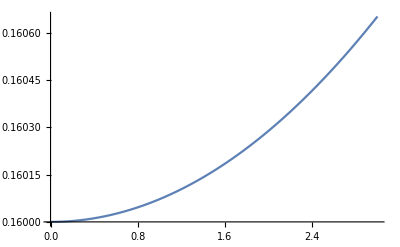

```mathematica
Tf^2== T0^2/(1-om^2x)
Solve[%,x]
```

```mathematica
CTensor[gamma{1,0,om,0},{cyl}]
ToCTensor[%,{mnk}]
```

CTensor[{1/(√(1-Ω^2 ρ^2)),0,Ω/(√(1-Ω^2 ρ^2)),0},{cyl},0]

CTensor[{1/(√(1-Ω^2 ρ^2)),-(Ω ρ Sin[ϕ])/(√(1-Ω^2 ρ^2)),(Ω Cos[ϕ] ρ)/(√(1-Ω^2 ρ^2)),0},{mnk},0]

```mathematica
u=CTensor[gamma{1,-om y[],om x[],0},{mnk},0]/.tomnk
```

CTensor[{1/(√(1-Ω^2 (x^2+y^2))),-(Ω y)/(√(1-Ω^2 (x^2+y^2))),(Ω x)/(√(1-Ω^2 (x^2+y^2))),0},{mnk},0]

```mathematica
gamma/.rho[]->9.4219719016026335/.om->0.030406373118000003
```

1.04375

CTensor[{1/(√(1-Ω^2 ρ^2)),-(Ω ρ Sin[ϕ])/(√(1-Ω^2 ρ^2)),(Ω Cos[ϕ] ρ)/(√(1-Ω^2 ρ^2)),0},{mnk},0]

Ω y

```mathematica
u/.om->0.030406373118000003/.rho[]->9.4219719016026335
ToCTensor[%,{mnk}]/.rho[]->9.4219719016026335
```

CTensor[{1.04375,-0.0317367 y,0.0317367 x,0},{mnk},0]

CTensor[{1.04375,-0.0317367 y,0.0317367 x,0},{mnk},0]

```mathematica
CTensorEntries[u]
```

T | 0
  | 1/(√(1-Ω^2 (x^2+y^2)))
T | 1
  | -(Ω y)/(√(1-Ω^2 (x^2+y^2)))
T | 2
  | (Ω x)/(√(1-Ω^2 (x^2+y^2)))

```mathematica
Assuming[om^2(x[]^2+y[]^2)<1,u/.tomnk//FullSimplify]
%/.{x[]->-9,om->0.03,y[]->1}
```

CTensor[{1/(√(1-Ω^2 (x^2+y^2))),-(Ω y)/(√(1-Ω^2 (x^2+y^2))),(Ω x)/(√(1-Ω^2 (x^2+y^2))),0},{mnk},0]

CTensor[{1.03908,-0.0311723,-0.280551,0},{mnk},0]

```mathematica
u/.tomnk/.x[]->-9.3219719016026339/.om->0.030406373118000003/.y[]->1.3690852348632359
```

CTensor[{1.04375,-0.0434502,-0.295848,0},{mnk},0]

Delta[m,n] 1/(√(1-Ω^2 ρ^2))
0
-(Ω ρ^2)/(√(1-Ω^2 ρ^2))
0 |  
ν

{{0,-0.00980001,0.00143929,0},{0,-0.000407964,0.0317966,0},{0,-0.0345144,0.000407964,0},{0,0,0,0}}

{1.04375,-0.0434502,-0.295848,0}

{5.42101×10^-20,-0.00938923,0.00137896,0.}

0.

```mathematica
CTensor[{0,1,0,0},{cyl}]
ToCTensor[%,{mnk}]
```

CTensor[{0,1,0,0},{cyl},0]

CTensor[{0,Cos[ϕ],Sin[ϕ],0},{mnk},0]

```mathematica
CD[-m]@u[-n];
CTensor[%[[0,1]],{-mnk,-mnk}]//FullSimplify;
%/.tomnk/.x[]->-9.3219719016026339/.y[]->1.3690852348632359/.om->0.030406373118000003
%[-m,-n][[0,1]]//MatrixForm
```

CTensor[{{0,-0.00980001,0.00143929,0},{0,-0.000407964,0.0317966,0},{0,-0.0345144,0.000407964,0},{0,0,0,0}},{-mnk,-mnk},0]

(0 | -0.00980001 | 0.00143929 | 0
0 | -0.000407964 | 0.0317966 | 0
0 | -0.0345144 | 0.000407964 | 0
0 | 0 | 0 | 0)

```mathematica
CD[-m]@u[-n]//FromBasisExpand;
CTensor[%[[0,1]],{-mnk,-mnk}];
CTensorEntries[%]
%%[-m,-n]
```

T |   |  
0 | 1 | (Ω^2 x)/((1-Ω^2 (x^2+y^2))^(3/2))
T |   |  
0 | 2 | (Ω^2 y)/((1-Ω^2 (x^2+y^2))^(3/2))
T |   |  
1 | 1 | (Ω^3 x y)/((1-Ω^2 (x^2+y^2))^(3/2))
T |   |  
1 | 2 | -(Ω (-1+Ω^2 x^2))/((1-Ω^2 (x^2+y^2))^(3/2))
T |   |  
2 | 1 | (Ω (-1+Ω^2 y^2))/((1-Ω^2 (x^2+y^2))^(3/2))
T |   |  
2 | 2 | -(Ω^3 x y)/((1-Ω^2 (x^2+y^2))^(3/2))

0 | (Ω^2 x)/((1-Ω^2 (x^2+y^2))^(3/2)) | (Ω^2 y)/((1-Ω^2 (x^2+y^2))^(3/2)) | 0
0 | (Ω^3 x y)/((1-Ω^2 (x^2+y^2))^(3/2)) | ● | 0
0 | ● | -(Ω^3 x y)/((1-Ω^2 (x^2+y^2))^(3/2)) | 0
0 | 0 | 0 | 0 |   |  
μ | ν

```mathematica
Ω^3 Cos[ϕ] ρ^2 Sin[ϕ]/.tomnk//FullSimplify
```

Ω^3 x y

```mathematica
CD[-m]@beta[-n];
CTensor[%[[0,1]],{-mnk,-mnk}]//FullSimplify
CTensorEntries[%]
```

CTensor[{{0,0,0,0},{0,0,Ω/T_0,0},{0,-Ω/T_0,0,0},{0,0,0,0}},{-mnk,-mnk},0]

T |   |  
1 | 2 | Ω/T_0

```mathematica
metric[m,n]-u[m]u[n]//Simplify;
%[[0,1]];
Delta=CTensor[%,{mnk,mnk}];
```

```mathematica
CTensorEntries[Delta]
%%[m,n]
```

T | 0 | 0
  |   | 1+1/(-1+Ω^2 (x^2+y^2))
T | 0 | 1
  |   | (Ω y)/(1-Ω^2 (x^2+y^2))
T | 0 | 2
  |   | (Ω x)/(-1+Ω^2 (x^2+y^2))
T | 1 | 1
  |   | (1-Ω^2 x^2)/(-1+Ω^2 (x^2+y^2))
T | 1 | 2
  |   | (Ω^2 x y)/(1-Ω^2 (x^2+y^2))
T | 2 | 2
  |   | (1-Ω^2 y^2)/(-1+Ω^2 (x^2+y^2))
T | 3 | 3
  |   | -1

1+1/(-1+Ω^2 (x^2+y^2)) | (Ω y)/(1-Ω^2 (x^2+y^2)) | (Ω x)/(-1+Ω^2 (x^2+y^2)) | 0
(Ω y)/(1-Ω^2 (x^2+y^2)) | (1-Ω^2 x^2)/(-1+Ω^2 (x^2+y^2)) | (Ω^2 x y)/(1-Ω^2 (x^2+y^2)) | 0
(Ω x)/(-1+Ω^2 (x^2+y^2)) | (Ω^2 x y)/(1-Ω^2 (x^2+y^2)) | (1-Ω^2 y^2)/(-1+Ω^2 (x^2+y^2)) | 0
0 | 0 | 0 | -1 | μ | ν
  |

(1-Ω^2 y^2)/(-1+Ω^2 (x^2+y^2))

```mathematica
ToCTensor[Delta,{mnk,-mnk}];
CTensorEntries[%]
%%[m,-n]
```

T | 0 |  
  | 0 | 1+1/(-1+Ω^2 (x^2+y^2))
T | 0 |  
  | 1 | (Ω y)/(-1+Ω^2 (x^2+y^2))
T | 0 |  
  | 2 | -(Ω x)/(-1+Ω^2 (x^2+y^2))
T | 1 |  
  | 0 | (Ω y)/(1-Ω^2 (x^2+y^2))
T | 1 |  
  | 1 | (-1+Ω^2 x^2)/(-1+Ω^2 (x^2+y^2))
T | 1 |  
  | 2
T | 2 |  
  | 1 | (Ω^2 x y)/(-1+Ω^2 (x^2+y^2))
T | 2 |  
  | 0 | (Ω x)/(-1+Ω^2 (x^2+y^2))
T | 2 |  
  | 2 | (-1+Ω^2 y^2)/(-1+Ω^2 (x^2+y^2))
T | 3 |  
  | 3 | 1

1+1/(-1+Ω^2 (x^2+y^2)) | (Ω y)/(-1+Ω^2 (x^2+y^2)) | -(Ω x)/(-1+Ω^2 (x^2+y^2)) | 0
(Ω y)/(1-Ω^2 (x^2+y^2)) | (-1+Ω^2 x^2)/(-1+Ω^2 (x^2+y^2)) | (Ω^2 x y)/(-1+Ω^2 (x^2+y^2)) | 0
(Ω x)/(-1+Ω^2 (x^2+y^2)) | (Ω^2 x y)/(-1+Ω^2 (x^2+y^2)) | (-1+Ω^2 y^2)/(-1+Ω^2 (x^2+y^2)) | 0
0 | 0 | 0 | 1 | μ |  
  | ν

```mathematica
Cos[ϕ]^2/(1-Ω^2 ρ^2)+Sin[ϕ]^2/.tomnk//FullSimplify
```

(-1+Ω^2 y^2)/(-1+Ω^2 (x^2+y^2))

```mathematica
ToCTensor[Delta,{-mnk,-mnk}];
CTensorEntries[%]
%%[-m,-n]
```

T |   |  
0 | 0 | 1+1/(-1+Ω^2 (x^2+y^2))
T |   |  
0 | 1 | (Ω y)/(-1+Ω^2 (x^2+y^2))
T |   |  
0 | 2 | -(Ω x)/(-1+Ω^2 (x^2+y^2))
T |   |  
1 | 1 | (1-Ω^2 x^2)/(-1+Ω^2 (x^2+y^2))
T |   |  
1 | 2 | -(Ω^2 x y)/(-1+Ω^2 (x^2+y^2))
T |   |  
2 | 2 | (1-Ω^2 y^2)/(-1+Ω^2 (x^2+y^2))
T |   |  
3 | 3 | -1

1+1/(-1+Ω^2 (x^2+y^2)) | (Ω y)/(-1+Ω^2 (x^2+y^2)) | -(Ω x)/(-1+Ω^2 (x^2+y^2)) | 0
(Ω y)/(-1+Ω^2 (x^2+y^2)) | (1-Ω^2 x^2)/(-1+Ω^2 (x^2+y^2)) | -(Ω^2 x y)/(-1+Ω^2 (x^2+y^2)) | 0
-(Ω x)/(-1+Ω^2 (x^2+y^2)) | -(Ω^2 x y)/(-1+Ω^2 (x^2+y^2)) | (1-Ω^2 y^2)/(-1+Ω^2 (x^2+y^2)) | 0
0 | 0 | 0 | -1 |   |  
μ | ν

```mathematica
Cos[ϕ]^2/(-1+Ω^2 ρ^2)-Sin[ϕ]^2/.tomnk//Simplify
```

(1-Ω^2 y^2)/(-1+Ω^2 (x^2+y^2))

```mathematica
u[m]CD[-m]@u[n];
ac=CTensor[%[[0,1]],{mnk}];
CTensorEntries[%]
```

T | 1
  | (Ω^2 x)/(-1+Ω^2 (x^2+y^2))
T | 2
  | (Ω^2 y)/(-1+Ω^2 (x^2+y^2))

```mathematica
-0.009800009482417025*-0.04345018157766605+0.0014392929334608047*-0.295848177653451
```

5.42101×10^-20

```mathematica
{{0,-0.009800009482417025,0.0014392929334608047,0},{0,-0.0004079637762623893,0.031796568147232085,0},{0,-0.03451443871686782,0.0004079637762623893,0},{0,0,0,0}}
{1.04375,-0.04345018157766605,-0.295848177653451,0}
%%.%
%%%[[2,1]]%%[[1]]+%%%[[2,2]]%%[[2]]+%%%[[2,3]]%%[[3]]+%%%[[2,4]]%%[[4]]
```

{{0,-0.00980001,0.00143929,0},{0,-0.000407964,0.0317966,0},{0,-0.0345144,0.000407964,0},{0,0,0,0}}

{1.04375,-0.0434502,-0.295848,0}

{5.42101×10^-20,-0.00938923,0.00137896,0.}

0.

```mathematica
Delta[-m,-n]/.x[]->-9.3219719016026339/.y[]->1.369085234863235/.om->0.030406373118000003;
%[[0,1]]//MatrixForm
```

(-0.0894141 | -0.0453511 | -0.308792 | 0
-0.0453511 | -1.00189 | -0.0128547 | 0
-0.308792 | -0.0128547 | -1.08753 | 0
0 | 0 | 0 | -1)

```mathematica
Delta[m,-n]/.x[]->-9.3219719016026339/.y[]->1.369085234863235/.om->0.030406373118000003;
%[[0,1]]//MatrixForm
```

(-0.0894141 | -0.0453511 | -0.308792 | 0
0.0453511 | 1.00189 | 0.0128547 | 0
0.308792 | 0.0128547 | 1.08753 | 0
0 | 0 | 0 | 1)

```mathematica
ac/.x[]->-9.3219719016026339/.y[]->1.369085234863235/.om->0.030406373118000003
```

CTensor[{0,0.00938923,-0.00137896,0},{mnk},0]

```mathematica
eps[m,n,a,b]u[-n]CD[-a]@u[-b]/2//FullSimplify
fvortvec=CTensor[%[[0,1]],{mnk}]
```

0
0
0
Ω/(-1+Ω^2 (x^2+y^2)) | μ

CTensor[{0,0,0,Ω/(-1+Ω^2 (x^2+y^2))},{mnk},0]

```mathematica
fvortvec/.x[]->-9.3219719016026339/.y[]->1.369085234863235/.om->0.030406373118000003
```

CTensor[{0,0,0,-0.0331251},{mnk},0]

```mathematica
gradu[m_,n_]:=(Delta[m,l]CD[-l]@u[n]//FromBasisExpand)//FullSimplify
```

```mathematica
CD[-m]@beta[-n]
```

0 | 0 | 0 | 0
0 | 0 | (Ω ρ)/T_0 | 0
0 | -(Ω ρ)/T_0 | 0 | 0
0 | 0 | 0 | 0 |   |  
ν | μ

```mathematica
gradu[-m,-n]/.x[]->-9.3219719016026339/.y[]->1.369085234863235/.om->0.030406373118000003;
%[[0,1]]//MatrixForm
```

(0 | 0.00980001 | -0.00143929 | 0
-0.00980001 | 0 | -0.0345744 | 0
0.00143929 | 0.0345744 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
-Antisymmetrize[CD[-m]@beta[-n],{-m,-n}];
CTensor[%[[0,1]],{-mnk,-mnk}];
CTensorEntries[%]
%%[-m,-n]
```

T |   |  
1 | 2 | Ω/T_0

0 | 0 | 0 | 0
0 | 0 | Ω/T_0 | 0
0 | -Ω/T_0 | 0 | 0
0 | 0 | 0 | 0 |   |  
μ | ν

```mathematica
gradu[-m,-n];
CTensor[%[[0,1]],{-cyl,-cyl}];
ToCTensor[%,{-mnk,-mnk}]//FullSimplify;
CTensorEntries[%]
%%[-m,-n]
```

T |   |  
0 | 1 | -(Ω^2 Cos[ϕ] ρ)/((1-Ω^2 ρ^2)^(3/2))
T |   |  
0 | 2 | -(Ω^2 ρ Sin[ϕ])/((1-Ω^2 ρ^2)^(3/2))
T |   |  
1 | 2 | -Ω/((1-Ω^2 ρ^2)^(3/2))

0 | -(Ω^2 Cos[ϕ] ρ)/((1-Ω^2 ρ^2)^(3/2)) | -(Ω^2 ρ Sin[ϕ])/((1-Ω^2 ρ^2)^(3/2)) | 0
(Ω^2 Cos[ϕ] ρ)/((1-Ω^2 ρ^2)^(3/2)) | 0 | -Ω/((1-Ω^2 ρ^2)^(3/2)) | 0
(Ω^2 ρ Sin[ϕ])/((1-Ω^2 ρ^2)^(3/2)) | Ω/((1-Ω^2 ρ^2)^(3/2)) | 0 | 0
0 | 0 | 0 | 0 |   |  
μ | ν

```mathematica
Antisymmetrize[gradu[-m,-n],{-m,-n}];
CTensor[%[[0,1]],{-cyl,-cyl}];
ToCTensor[%,{-mnk,-mnk}]//FullSimplify;
CTensorEntries[%]
%%[-m,-n]
```

T |   |  
0 | 1 | -(Ω^2 Cos[ϕ] ρ)/((1-Ω^2 ρ^2)^(3/2))
T |   |  
0 | 2 | -(Ω^2 ρ Sin[ϕ])/((1-Ω^2 ρ^2)^(3/2))
T |   |  
1 | 2 | -Ω/((1-Ω^2 ρ^2)^(3/2))

0 | -(Ω^2 Cos[ϕ] ρ)/((1-Ω^2 ρ^2)^(3/2)) | -(Ω^2 ρ Sin[ϕ])/((1-Ω^2 ρ^2)^(3/2)) | 0
(Ω^2 Cos[ϕ] ρ)/((1-Ω^2 ρ^2)^(3/2)) | 0 | -Ω/((1-Ω^2 ρ^2)^(3/2)) | 0
(Ω^2 ρ Sin[ϕ])/((1-Ω^2 ρ^2)^(3/2)) | Ω/((1-Ω^2 ρ^2)^(3/2)) | 0 | 0
0 | 0 | 0 | 0 |   |  
μ | ν

```mathematica
1/2 eps[m,n,a,b]u[-n]CD[-a]@u[-b]//Simplify;
CTensor[%[[0,1]],{cyl}];
ToCTensor[%,{mnk}]//FullSimplify;
CTensorEntries[%]
```

T | 3
  | Ω/(-1+Ω^2 ρ^2)

T | 3
  | Ω/(-1+Ω^2 ρ^2)